## Задание 1 номер 1

```mathematica
t1=(6(x^3-8)(x^2-y^2))/(2 x^2-8)+(x+y)^2+x^3+y^3
```

x^3+y^3+(x+y)^2+(6 (-8+x^3) (x^2-y^2))/(-8+2 x^2)

```mathematica
Expand[t1]
```

x^2+x^3-(48 x^2)/(-8+2 x^2)+(6 x^5)/(-8+2 x^2)+2 x y+y^2+(48 y^2)/(-8+2 x^2)-(6 x^3 y^2)/(-8+2 x^2)+y^3

```mathematica
ExpandAll[t1]
```

x^2+x^3-(48 x^2)/(-8+2 x^2)+(6 x^5)/(-8+2 x^2)+2 x y+y^2+(48 y^2)/(-8+2 x^2)-(6 x^3 y^2)/(-8+2 x^2)+y^3

```mathematica
Factor[t1]
```

((x+y) (14 x+9 x^2+4 x^3-10 y-7 x y-4 x^2 y+2 y^2+x y^2))/(2+x)

```mathematica
Together[t1]
```

(14 x^2+9 x^3+4 x^4+4 x y+2 x^2 y-10 y^2-5 x y^2-3 x^2 y^2+2 y^3+x y^3)/(2+x)

```mathematica
Apart[t1]
```

(x^2 (14+9 x+4 x^2))/(2+x)+2 x y-((10+5 x+3 x^2) y^2)/(2+x)+y^3

```mathematica
Cancel[t1]
```

x^3+y^3+(x+y)^2+(3 (4+2 x+x^2) (x^2-y^2))/(2+x)

```mathematica
Simplify[t1]
```

x^3+y^3+(x+y)^2+(3 (4+2 x+x^2) (x^2-y^2))/(2+x)

## Задание 1 номер 2

```mathematica
t2=Numerator[t1]
```

x^3+y^3+(x+y)^2+(6 (-8+x^3) (x^2-y^2))/(-8+2 x^2)

```mathematica
Collect[t2,x]
```

x^3+y^3+(x+y)^2+(6 (-8+x^3) (x^2-y^2))/(-8+2 x^2)

```mathematica
Collect[t2,y]
```

x^2+x^3+(6 x^2 (-8+x^3))/(-8+2 x^2)+2 x y+(1-(6 (-8+x^3))/(-8+2 x^2)) y^2+y^3

```mathematica
Exponent[t2,x]
```

5

```mathematica
Exponent[t2,y]
```

3

```mathematica
For[i=0,i<=Exponent[t2,x],i=i+1, Print["Coefficient[t2, x, ", i,"] = ", Coefficient[t2,x,i]]]
```

Coefficient[t2, x, 0] = -5 y^2+y^3

Coefficient[t2, x, 1] = 12+2 y-3 y^2

Coefficient[t2, x, 2] = 1

Coefficient[t2, x, 3] = 4

Coefficient[t2, x, 4] = 0

Coefficient[t2, x, 5] = 0

```mathematica
For[i=0,i<=Exponent[t2,y],i=i+1, Print["Coefficient[t2, y, ", i,"] = ", Coefficient[t2,y,i]]]
```

Coefficient[t2, y, 0] = x^2+x^3-(48 x^2)/(-8+2 x^2)+(6 x^5)/(-8+2 x^2)

Coefficient[t2, y, 1] = 2 x

Coefficient[t2, y, 2] = 1+48/(-8+2 x^2)-(6 x^3)/(-8+2 x^2)

Coefficient[t2, y, 3] = 1

## Задание 2 номер 1

```mathematica
D[x^n Cos[x], x]
```

n x^(-1+n) Cos[x]-x^n Sin[x]

## Задание 2 номер 2

```mathematica
D[(a x^3+2 x^2), x]
```

4 x+3 a x^2

```mathematica
D[4 x^2-5x+8-3/x,{x,3}]
```

18/x^4

```mathematica
D[x^3 y^2+3 x^2, {x,3},{y,2}]
```

12

## Задание 2 номер 3

```mathematica
∫1/(x^2-1)ⅆx
```

1/2 Log[1-x]-1/2 Log[1+x]

## Задание 2 номер 4

```mathematica
∫x^3/(x^2+1)ⅆx
```

x^2/2-1/2 Log[1+x^2]

```mathematica
Together[D[(∫x^3/(x^2+1)ⅆx), x]]
```

x^3/(1+x^2)

```mathematica
∫1/(x^3+1)ⅆx
```

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
ExpandAll[Together[D[(∫1/(x^3+1)ⅆx), x]]]
```

1/(1+x^3)

## Задание 2 номер 5

```mathematica
∫_1^4 (5x-2 √x+32/x^3)ⅆx
```

259/6

## Задание 2 номер 6

```mathematica
∫_0^1 (1+x^4)^(1/3)ⅆx
```

Hypergeometric2F1[-1/3,1/4,5/4,-1]

```mathematica
∫_0^1. (1+x^4)^(1/3)ⅆx
```

1.05753

## Задание 3 номер 1

```mathematica
Solve[a x^4+x^2+3==0,x]
```

{{x→-(√(-1/a-(√(1-12 a))/a))/(√2)},{x→(√(-1/a-(√(1-12 a))/a))/(√2)},{x→-(√(-1/a+(√(1-12 a))/a))/(√2)},{x→(√(-1/a+(√(1-12 a))/a))/(√2)}}

## Задание 3 номер 2

```mathematica
Solve[x^2+y==1&&y^2-x^2==2, {x,y}]
```

{{x→-ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→ⅈ √(1/2 (-3+√13)),y→1/2 (-1+√13)},{x→-√(1/2 (3+√13)),y→1/2 (-1-√13)},{x→√(1/2 (3+√13)),y→1/2 (-1-√13)}}

```mathematica
NSolve[x^2+y==1&&y^2-x^2==2, {x,y}]
```

{{x→-1.81735,y→-2.30278},{x→0.-0.550251 ⅈ,y→1.30278},{x→0.+0.550251 ⅈ,y→1.30278},{x→1.81735,y→-2.30278}}

## Задание 3 номер 3

```mathematica
Solve[x^2-y^2==1&&y^3+x==5,{x,y}]
```

{{x→5-(Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025)^3,y→Root1.48Root[24-#1^2-10 #1^3+#1^6&,1]1.4762125973105025},{x→5-(Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715)^3,y→Root1.93Root[24-#1^2-10 #1^3+#1^6&,2]1.9285042654455715},{x→5-(Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702)^3,y→Root-0.914-1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,3]-0.91389935476702},{x→5-(Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702)^3,y→Root-0.914+1.30 ⅈRoot[24-#1^2-10 #1^3+#1^6&,4]-0.91389935476702},{x→5-(Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017)^3,y→Root-0.788-1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,5]-0.788459076611017},{x→5-(Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017)^3,y→Root-0.788+1.65 ⅈRoot[24-#1^2-10 #1^3+#1^6&,6]-0.788459076611017}}

```mathematica
NSolve[x^2-y^2==1&&y^3+x==5,{x,y}]
```

{{x→-0.928941-1.39823 ⅈ,y→-0.788459-1.64735 ⅈ},{x→-0.928941+1.39823 ⅈ,y→-0.788459+1.64735 ⅈ},{x→1.78303,y→1.47621},{x→-2.17236,y→1.9285},{x→1.1236-1.05808 ⅈ,y→-0.913899+1.30087 ⅈ},{x→1.1236+1.05808 ⅈ,y→-0.913899-1.30087 ⅈ}}

## Задание 3 номер 4

```mathematica
DSolve[y'[x]-y[x]Tan[x]==x,y[x],x]
```

{{y[x]→C[1] Sec[x]+Sec[x] (Cos[x]+x Sin[x])}}

```mathematica
DSolve[y'[x]+y[x]Tan[x]==1/Cos[x],y[x],x]
```

{{y[x]→C[1] Cos[x]+Sin[x]}}

## Задание 3 номер 5

```mathematica
DSolve[y''[x]-y'[x]+x y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(x/2) AiryAi[-(-1)^(1/3) (1/4-x)] C[1]+ⅇ^(x/2) AiryBi[-(-1)^(1/3) (1/4-x)] C[2]}}

```mathematica
w1=DSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==1, y'[0]==1},y[x],x]
```

{{y[x]→(ⅇ^(x/2) (-(-1)^(2/3) AiryAi[-(-1)^(1/3) (1/4-x)] AiryBi[-1/4 (-1)^(1/3)]+(-1)^(2/3) AiryAi[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]+2 AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (1/4-x)]-2 AiryAi[-(-1)^(1/3) (1/4-x)] AiryBiPrime[-1/4 (-1)^(1/3)]))/(2 (AiryAiPrime[-1/4 (-1)^(1/3)] AiryBi[-1/4 (-1)^(1/3)]-AiryAi[-1/4 (-1)^(1/3)] AiryBiPrime[-1/4 (-1)^(1/3)]))}}

```mathematica
w2=NDSolve[{y''[x]-y'[x]+x y[x]==0,y[0]==1, y'[0]==1},y[x],{x, -10, 10}]
```

{{y[x]→InterpolatingFunction[…][x]}}

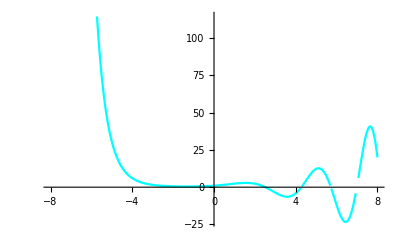

```mathematica
Plot[w1[[1,1,2]],{x,-8,8}, PlotStyle->Cyan]
```

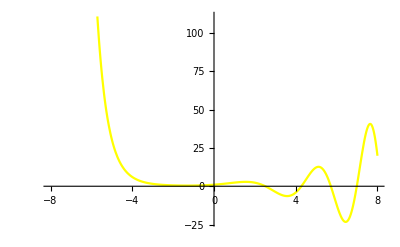

```mathematica
Plot[w2[[1,1,2]],{x,-8,8}, PlotStyle->Yellow]
```